# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 1

## 1.1 BASIC DEFINITIONS

### 1.1.3 Mathematica Implementation

```mathematica
psi1DPIB[n_,x_,L_]:=Sqrt[2/L]*Sin[n*Pi*x/L];energy1DPIB[n_,L_]:=(hbar^2*Pi^2*n^2)/(2*m*L^2);
```

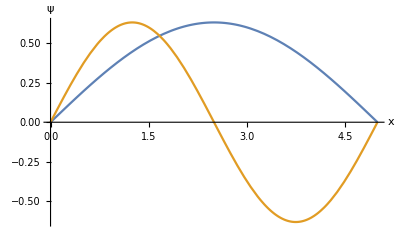

```mathematica
hbar=1; (*define variables in atomic units*)
m=1;(*set m=1 me, i.e., units of electron mass, me*)
L=5; (*set L=5 a0, i.e., units of Bohr radii, a0*)
g1=Plot[
{psi1DPIB[1,x,L],psi1DPIB[2,x,L]},
{x,0,L},AxesLabel->{"x","ψ"}]
```

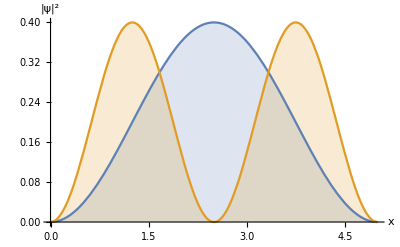

```mathematica
g2=Plot[
{Conjugate[psi1DPIB[1,x,L]]*psi1DPIB[1,x,L],Conjugate[psi1DPIB[2,x,L]]*psi1DPIB[2,x,L]},
{x,0,L},AxesLabel->{"x","|ψ|^2"},Filling->Axis]
```

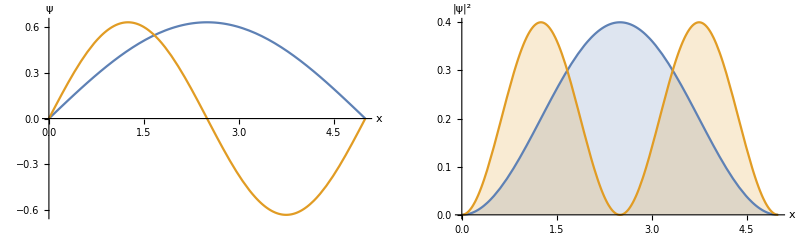

```mathematica
GraphicsRow[{g1,g2}]
```

## 1.2 USING SYMBOLIC AND NUMERICAL INTEGRATION

### 1.2.1 Wavefunction orthonormality

```mathematica
Integrate[Conjugate[psi1DPIB[1,x,L]]*psi1DPIB[1,x,L],{x,0,L}]
```

1

```mathematica
NIntegrate[Conjugate[psi1DPIB[1,x,L]]*psi1DPIB[1,x,L],{x,0,L}]
```

1.

```mathematica
Integrate[Conjugate[psi1DPIB[2,x,L]]*psi1DPIB[1,x,L],{x,0,L}]
```

0

```mathematica
NIntegrate[Conjugate[psi1DPIB[2,x,L]]*psi1DPIB[1,x,L],{x,0,L}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.72063}. NIntegrate obtained -1.21431×10^-17 and 1.12868×10^-16 for the integral and error estimates.

-1.21431×10^-17

### 1.2.2 Calculating position probabilities

```mathematica
Clear[m,hbar,n,x,L];
Integrate[
Conjugate[psi1DPIB[n,x,L]]*psi1DPIB[n,x,L],{x,xmin,xmax}]
```

∫_xmin^xmax 2 √(1/L) Conjugate[√(1/L)] Sin[(n π x)/L] Sin[(π Conjugate[n x])/Conjugate[L]]ⅆx

```mathematica
Integrate[
Conjugate[psi1DPIB[n,x,L]]*psi1DPIB[n,x,L],{x,xmin,xmax},Assumptions-> Element[n,Integers]&&n>0&&
Element[L,Reals]&&L>0&&Element[x,Reals]&&x≥0]
```

(2 n π (xmax-xmin)-5 Sin[(2 n π xmax)/5]+5 Sin[(2 n π xmin)/5])/(10 n π)

```mathematica
%/.{L->5,xmax->2.5,xmin->0,n->1}
```

0.5

### 1.2.3 Energy eigenvalues

```mathematica
Clear[m,hbar,n,x,L];
Integrate[
Conjugate[psi1DPIB[n,x,L]]*(-hbar^2/(2*m))*D[D[psi1DPIB[n,x,L],x],x],{x,0,L},
Assumptions->Element[n,Integers]&&n>0&&
Element[L,Reals]&&L>0&&Element[x,Reals]&&x≥0]
```

(hbar^2 n π (2 n π-Sin[2 n π]))/(4 L^2 m)

```mathematica
%/.Sin[2*n*Pi]->0
```

(hbar^2 n^2 π^2)/(2 L^2 m)

### 1.2.4 Expectation values

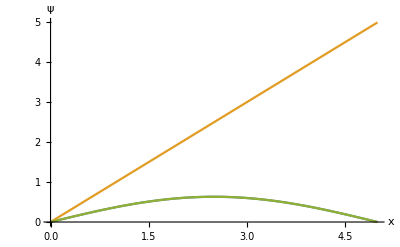

```mathematica
hbar=1;m=1;L=5;
Plot[
{Conjugate[psi1DPIB[1,x,L]],x,psi1DPIB[1,x,L]},
{x,0,L},AxesLabel->{"x","ψ"}]
```

```mathematica
NIntegrate[Conjugate[psi1DPIB[1,x,L]]*x*psi1DPIB[1,x,L],{x,0,L}]
```

2.5

## 1.3 SUPERPOSITIONS

```mathematica
equalSuperposition[x_,L_]:=(1/Sqrt[2])*(psi1DPIB[1,x,L]+psi1DPIB[2,x,L]);
```

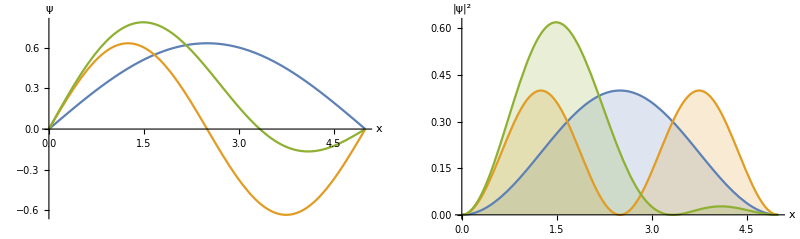

```mathematica
hbar=1;m=1;L=5;
GraphicsRow[
{Plot[
{psi1DPIB[1,x,L],psi1DPIB[2,x,L],equalSuperposition[x,L]},
{x,0,L},AxesLabel->{"x","ψ"}],
Plot[
{Conjugate[psi1DPIB[1,x,L]]*psi1DPIB[1,x,L],Conjugate[psi1DPIB[2,x,L]]*psi1DPIB[2,x,L],Conjugate[equalSuperposition[x,L]]*equalSuperposition[x,L]},
{x,0,L},AxesLabel->{"x","|ψ|^2"},Filling->Axis]}]
```

```mathematica
NIntegrate[
Conjugate[equalSuperposition[x,L]]*equalSuperposition[x,L],{x,0,L}]
```

1.

## 1.4 DEGENERACY: THE 2D PARTICLE IN A BOX

```mathematica
psi2DPIB[nx_,ny_,x_,y_,Lx_,Ly_]:=psi1DPIB[nx,x,Lx]*psi1DPIB[ny,y,Ly];energy2DPIB[nx_,ny_,Lx_,Ly_]:=energy1DPIB[nx,Lx]+energy1DPIB[ny,Ly];
```

```mathematica
hbar=1;m=1;L=5;
GraphicsRow[
{Plot3D[psi2DPIB[1,2,x,y,L,L],{x,0,L},{y,0,L}],Plot3D[Conjugate[psi2DPIB[1,2,x,y,L,L]]*psi2DPIB[1,2,x,y,L,L],{x,0,L},{y,0,L}]}]
```

-Graphics-

```mathematica
GraphicsRow[
{Plot3D[psi2DPIB[2,1,x,y,L,L],{x,0,L},{y,0,L}],Plot3D[Conjugate[psi2DPIB[2,1,x,y,L,L]]*psi2DPIB[2,1,x,y,L,L],{x,0,L},{y,0,L}]}]
```

-Graphics-

```mathematica
{energy2DPIB[1,2,L,L],energy2DPIB[2,1,L,L]}
```

{π^2/10,π^2/10}

```mathematica
Integrate[
Conjugate[psi2DPIB[1,2,x,y,L,L]]*psi2DPIB[1,2,x,y,L,L],
{x,0,L},{y,0,L}]
```

1

```mathematica
Integrate[
Conjugate[psi2DPIB[2,1,x,y,L,L]]*psi2DPIB[1,2,x,y,L,L],{x,0,L},{y,0,L}]
```

0

## 1.5 VISUALIZING PROBABILITY DENSITIES

```mathematica
psiSquared1DPIB[n_,x_,L_]:=Conjugate[psi1DPIB[n,x,L]]*psi1DPIB[n,x,L];
```

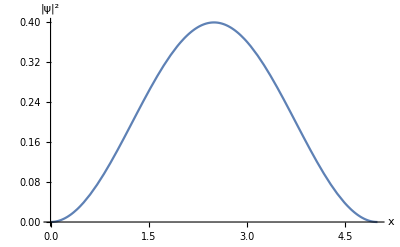

```mathematica
L=5;
exact=Plot[psiSquared1DPIB[1,x,L],{x,0,L},AxesLabel->{"x","|ψ|^2"}]
```

### 1.5.2 Implementation in Mathematica

```mathematica
acceptedPoints={};
Do[
If[psiSquared1DPIB[1,x=RandomReal[{0,L}],L]≥RandomReal[{0,0.5}],AppendTo[acceptedPoints,x]
]
,{10000}]
```

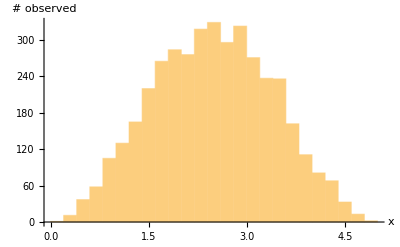

```mathematica
Histogram[acceptedPoints,PlotRange->{{0,L},{0,All}},AxesLabel->{"x","# observed"}]
```

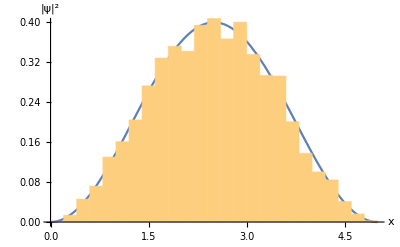

```mathematica
hist=Histogram[acceptedPoints,Automatic,"PDF",
PlotRange->{{0,L},{0,All}}];
Show[exact,hist]
```

### 1.5.3 Probability cloud visualization

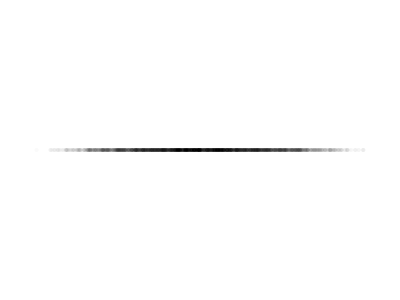

```mathematica
acceptedPointsChart={};
Do[
AppendTo[acceptedPointsChart,{Black,Opacity[0.02],Point[{acceptedPoints[[i]],0}]}],{i,1,Length[acceptedPoints]}]
Graphics[acceptedPointsChart]
```

```mathematica
psi3DPIB[nx_,ny_,nz_,x_,y_,z_,Lx_,Ly_,Lz_]:=psi1DPIB[nx,x,Lx]*psi1DPIB[ny,y,Ly]*psi1DPIB[nz,z,Lz];

psiSquared3DPIB[nx_,ny_,nz_,x_,y_,z_,Lx_,Ly_,Lz_]:=Conjugate[psi3DPIB[nx,ny,nz,x,y,z,Lx,Ly,Lz]]*psi3DPIB[nx,ny,nz,x,y,z,Lx,Ly,Lz];
```

```mathematica
L=5;
acceptedPointsChart={};
Do[If[psiSquared3DPIB[2,2,2,x=RandomReal[{0,L}],y=RandomReal[{0,L}],z=RandomReal[{0,L}],L,L,L]≥RandomReal[{0,0.5}],AppendTo[acceptedPointsChart,{Black,Point[{x,y,z}]}];],
{100000}]
Graphics3D[acceptedPointsChart]
```

-Graphics3D-

### 1.5.4 Isocontour surfaces visualization

```mathematica
ContourPlot3D[psiSquared3DPIB[2,2,2,x,y,z,L,L,L]==0.01,{x,0,L},{y,0,L},{z,0,L}]
```

-Graphics3D-

## 1.6 TIME-DEPENDENT WAVEFUNCTIONS

```mathematica
psi1DPIB[n_,x_,L_,t_]:=Exp[-I*energy1DPIB[n,L]*t/hbar]*psi1DPIB[n,x,L];equalSuperposition[x_,L_,t_]:=(1/Sqrt[2])*(psi1DPIB[1,x,L,t]+psi1DPIB[2,x,L,t]);
```

Erratum: (first printing)  Mathematica 11 is a bit stricter about evaluation, which breaks the code in the first printing.   Below is an alternate version that will appear in the second printing:

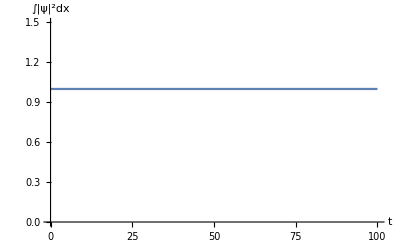

```mathematica
hbar=1; m=1; L=5; (*define mass and length in atomic units*)

(*define the integral to plot*)
intX[L_,t_]:=NIntegrate[Conjugate[equalSuperposition[x,L,t]]*
equalSuperposition[x,L,t],{x,0,L}]

Plot[
intX[L,t],{t,0,100},
AxesLabel-> {"t","∫|ψ|^2dx"},PlotRange->{0,1.5},AxesOrigin->{0,0}]
```

Erratum: Alternatively, a small modification (changing the

```mathematica
hbar=1; m=1; L=5; (*define mass and length in atomic units*)
Plot[
{NIntegrate[Conjugate[equalSuperposition[xx,L,t]]*
equalSuperposition[xx,L,t],{xx,0,L}]},{t,0,100},
AxesLabel-> {"t","∫|ψ|^2dx"},PlotRange->{0,1.5},AxesOrigin->{0,0}]
```

-Graphics-

Note:  This is an alternate version that does not appear in the text

```mathematica
hbar=1;m=1;L=5;(*define mass and length in atomic units*)
Animate[Plot[
{Conjugate[psi1DPIB[1,x,L,t]]*psi1DPIB[1,x,L,t],Conjugate[psi1DPIB[2,x,L,t]]*psi1DPIB[2,x,L,t],Conjugate[equalSuperposition[x,L,t]]*equalSuperposition[x,L,t]},{x,0,L},AxesLabel->{"x","|ψ|^2"},Filling->Axis,PlotRange->{0,1}],{t,0,100}]
```